# Numerical solution of Schrödinger equation for arbitrary N-dimensional potentials

## Jens Uwe Nöckel, University of Oregon [http://pages.uoregon.edu/noeckel/]. http://mathematica.stackexchange.com/questions/50763/schroedinger-eigenvalue-problem-in-two-dimensions-harmonic-oscillator

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/souda/Documents/Git-Codes/MathPCET

## test the new MathPCET package

```mathematica
Needs["MathPCET`"]
```

## Simple approach

```mathematica
?GridSolverND
```

### Test one-dimensional harmonic oscillator:

```mathematica
xx=10.0;
nX=128;
dx=xx/(2nX)
v1[x_]:=1/2 x^2;
v1Grid=Table[v1[dx i],{i,-nX,nX}];
```

0.0390625

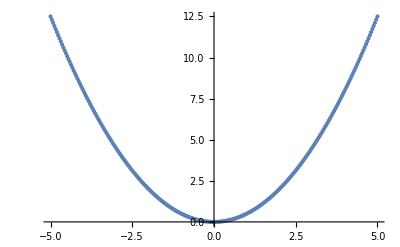

```mathematica
ListPlot[v1Grid,DataRange->{-nX dx,nX dx}]
```

```mathematica
sol1D=GridSolverND[v1Grid,dx,5,M->MassE];
```

```mathematica
sol1D⟦1⟧
```

{0.499952,1.49976,2.49938,3.49881,4.49805}

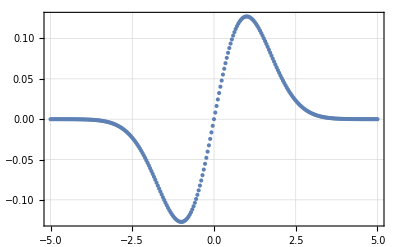

```mathematica
ListPlot[sol1D⟦2,2⟧,PlotRange->All,PlotTheme->"Detailed",DataRange->{-nX dx,nX dx}]
```

### Test one-dimensional unharmonic (from 2×2) oscillator:

```mathematica
xx=10.0;
nX=128;
dx=xx/(2nX);
v1u[x_]:=Module[{h1,h2,V=0.1,Δ=0.01},
h1=1/2 x^2;
h2=1/10 x^2+Δ;
1/2(h1+h2)-1/2 √((h1-h2)^2+4 V^2)
];
v1uGrid=Table[v1u[dx i],{i,-nX,nX}];
```

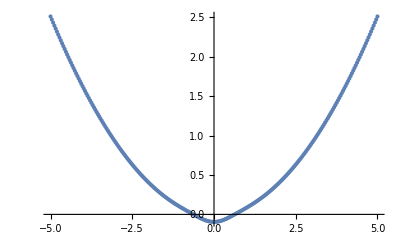

```mathematica
ListPlot[v1uGrid,DataRange->{-nX dx,nX dx}]
```

```mathematica
sol1D=GridSolverND[v1uGrid,dx,5,M->MassE];
```

```mathematica
sol1D⟦1⟧
```

{0.183177,0.66568,1.11119,1.58028,2.07172}

```mathematica
Manipulate[ListPlot[sol1D⟦2,i⟧,PlotRange->All,PlotTheme->"Detailed",DataRange->{-nX dx,nX dx}],{i,1,5,1}]
```

### Test two-dimensional harmonic oscillator:

```mathematica
nX=100;
nY=100;
a=.05;
```

```mathematica
v2[x_,y_]:=1/2(x^2+y^2)-10;
```

```mathematica
v2Grid=Table[v2[a i,a j],{i,-nX,nX},{j,-nY,nY}];
```

```mathematica
sol2D=GridSolverND[v2Grid,a,5,M->MassE];
```

```mathematica
sol2D⟦1⟧
```

{-9.00016,-8.00047,-8.00047,-7.00109,-7.00078}

```mathematica
ListContourPlot[sol2D⟦2,2⟧,PlotRange->All,Axes->False,DataRange->{{-a nX,a nX},{-a nX,a nX}}]
```

-Graphics-

```mathematica
ListPlot3D[-sol2D⟦2,2⟧,PlotRange->All,Boxed->False,Axes->False]
```

-Graphics3D-

### Test two-dimensional unharmonic (from 2×2) oscillator:

```mathematica
nX=100;
nY=100;
a=.05;
```

```mathematica
v2u[x_,y_]:=Module[{h1,h2,V=0.1,Δ=0.05},
h1=1/2(x^2+y^2);
h2=1/2 x^2+1/20 y^2+Δ;
1/2(h1+h2)-1/2 √((h1-h2)^2+4 V^2)
];
```

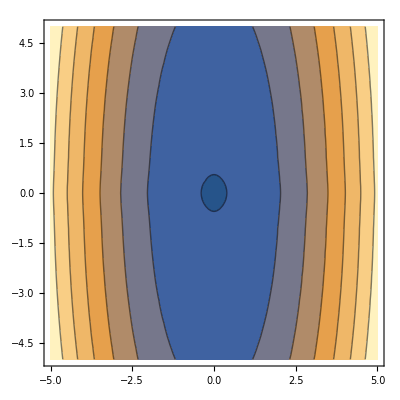

```mathematica
ContourPlot[v2u[x,y],{x,-5,5},{y,-5,5}]
```

```mathematica
v2Grid=Table[v2u[a i,a j],{i,-nX,nX},{j,-nY,nY}];
```

```mathematica
sol2D=GridSolverND[v2Grid,a,5,M->MassE];
```

```mathematica
sol2D⟦1⟧
```

{0.656811,1.01641,1.34279,1.6565,1.72993}

```mathematica
Manipulate[ListContourPlot[sol2D⟦2,i⟧,PlotRange->All,Axes->False,DataRange->{{-a nX,a nX},{-a nX,a nX}}],{i,1,5,1}]
```

Part::partd: Part specification sol2D⟦2,2⟧ is longer than depth of object.

DataRange::invdrange: {{-128. a,128. a},{-128. a,128. a}} must be of the form {xmin, xmax}.

ListContourPlot::arrayerr: sol2D⟦2,2⟧ must be a valid array.

```mathematica
ListPlot3D[-sol2D⟦2,2⟧,PlotRange->All,Boxed->False,Axes->False]
```

-Graphics3D-

### Test three-dimensional harmonic oscillator:

```mathematica
nX=16;
nY=16;
nZ=16;
a=0.3;
```

```mathematica
v3[x_,y_,z_]:=1/2(x^2+y^2+z^2);
```

```mathematica
v3Grid=Table[v3[a i,a j,a k],{i,-nX,nX},{j,-nY,nY},{k,-nZ,nZ}];
```

```mathematica
sol3D=GridSolverND[v3Grid,a,5,M->MassE];
```

```mathematica
sol3D⟦1⟧
```

{1.49151,2.48013,2.48013,3.4572,3.46875}

## General approach with an arbitrary difference order for the numerical second derivative

```mathematica
?GenGridSolverND
```

### Test 2D harmonic oscillator:

```mathematica
nX=200;
nY=200;
a=.025;
Clear[v2];
v2[x_,y_]:=1/2(x^2+y^2+x y)-10;
v2Grid=Table[v2[a i,a j],{i,-nX,nX},{j,-nY,nY}];
```

```mathematica
sol2ND=GenGridSolverND[v2Grid,a,5,M->MassE,DiffOrder->4];
```

```mathematica
sol2ND⟦1⟧
```

{-9.03407,-8.32697,-7.80933,-7.61986,-7.10222}

```mathematica
GraphicsRow[{
ListContourPlot[sol2ND⟦2,4⟧,PlotRange->All,ColorFunction->"DarkRainbow"],
ListContourPlot[sol2ND⟦2,5⟧,PlotRange->All,ColorFunction->"DarkRainbow"]
},ImageSize->Large]
```

-Graphics-

```mathematica
GraphicsRow[{
ListPlot3D[sol2ND⟦2,4⟧,PlotRange->All,Boxed->False,Axes->False,Mesh->25,ColorFunction->"DarkRainbow"],
ListPlot3D[sol2ND⟦2,5⟧,PlotRange->All,Boxed->False,Axes->False,Mesh->25,ColorFunction->"DarkRainbow"]
},ImageSize->Large]
```

-Graphics-

## Test FGH vibronic couplings

```mathematica
?FGHVibronicCouplings
```

```mathematica
testSolution=FGHVibronicCouplings["potential.dat",256,5];
```

```mathematica
potentialLeft=testSolution⟦1⟧⟦2⟧;
potentialRight=testSolution⟦2,2⟧;
```

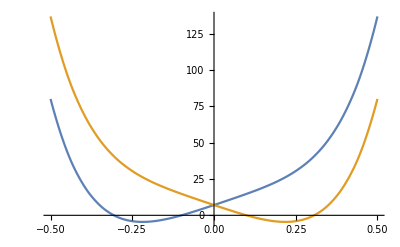

```mathematica
ListLinePlot[{potentialLeft,potentialRight}]
```

```mathematica
waveFunctionsLeft=testSolution⟦1,3⟧;
waveFunctionsRight=testSolution⟦2,3⟧;
```

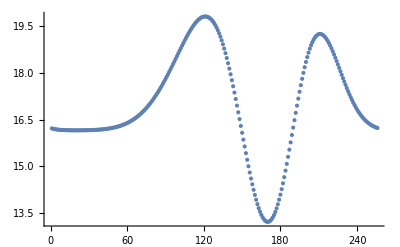

```mathematica
ListPlot[waveFunctionsRight⟦3⟧]
```

```mathematica
overlaps=testSolution⟦3⟧//TableForm
```

0.0560781 | -0.195449 | 0.410517 | 0.559661 | 0.529858
-0.195448 | 0.431643 | -0.491533 | -0.192225 | 0.232543
-0.410518 | 0.491534 | -0.103117 | 0.335931 | 0.274855
0.559665 | -0.192223 | -0.335933 | -0.187347 | 0.272443
0.529857 | 0.23255 | -0.274851 | 0.272446 | 0.189888

```mathematica
kappas=testSolution⟦11⟧//TableForm
```

0.22453 | 0.30141 | 0. | 0. | 0.
0.305758 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.